## Initializing

```mathematica
dirStr = NotebookDirectory[]~StringJoin~"Utils.nb";

NotebookEvaluate[dirStr];
NotebookEvaluate[dirStr];
(*Evaluates the Utils notebook which contains modules for calculating the QNF*)
```

```mathematica
(*We specify the Hamiltonian in pieces*)
term1 = p[1]^2/(2m) - 1/2 m ω[1]^2 q[1]^2 + p[2]^2/(2m) + 1/2 m ω[2]^2 q[2]^2 + p[3]^2/(2m) + 1/2 m ω[3]^2 q[3]^2;
term2 = 0;
term3 = g4[1] q[1]^4 /4! + g4[2] q[2]^4 /4! + g4[3] q[3]^4 /4! + λ4[1, 2] q[1]^2 q[2]^2 /4! + λ4[1, 3] q[1]^2 q[3]^2 /4!;

eigs = {-I ω[1], ω[2], ω[3]};
prs = {{p[1], q[1]}, {p[2], q[2]}, {p[3], q[3]}};

(*Some symplectic transformations used below. x' = (x - I p)/√2 = Sqrt[ℏ] a^† (the raising operator).
Similarly, p' = (p - I x)/√2 = -I Sqrt[ℏ] a (lowering operator).*)
scaleRule = {q[1] -> q[1]/Sqrt[m ω[1]],
			p[1] -> Sqrt[m ω[1]]p[1],
			q[2] -> q[2]/Sqrt[m ω[2]],
			p[2] -> Sqrt[m ω[2]]p[2],
			q[3] -> q[3]/Sqrt[m ω[3]],
			p[3] -> Sqrt[m ω[3]]p[3]};
diagRule = {q[1] -> I/Sqrt[2](q[1] + p[1]),
			p[1] -> -I/Sqrt[2](p[1] - q[1]),
			q[2] -> 1/Sqrt[2](q[2] + I p[2]),
			p[2] -> 1/Sqrt[2](p[2] + I q[2]),
			q[3] -> 1/Sqrt[2](q[3] + I p[3]),
			p[3] -> 1/Sqrt[2](p[3] + I q[3])};

(*Choose degeneracy:*)
(*Ω = ω;*)

(*We rescale and diagonalize the Hamiltonian, what we obtain we assign to H[n, m].
Here, n is the order of the term and m is the order of the QNF, which starts at 2.*)
H[0, 2] = 0;
H[1, 2] = 0;
H[2, 2] = Expand[term1 /. scaleRule /. diagRule];
H[3, 2] = Expand[term2 /. scaleRule /. diagRule];
H[4, 2] = Expand[term3 /. scaleRule /. diagRule];
H[n_ ? (# > 4 &), 2] := 0;

H[2, 2]
H[3, 2]
H[4, 2]

QNFOrd = 4;
QNFSymb = computeQNFSymbUpToOrder[QNFOrd]

success = Table[MB[QNFSymb[[3]], QNFSymb[[k]]], {k, 1, Length[QNFSymb]}] == ConstantArray[0, QNFOrd + 1]

If[success,
	Print["Normalization was successful, saving to file..."];
	saveDir = NotebookDirectory[]~StringJoin~"QNF.wl";
	Save[saveDir, {prs, QNFSymb}]
]
```

p[1] q[1] ω[1]+ⅈ p[2] q[2] ω[2]+ⅈ p[3] q[3] ω[3]

0

(g4[1] p[1]^4)/(96 m^2 ω[1]^2)+(g4[1] p[1]^3 q[1])/(24 m^2 ω[1]^2)+(g4[1] p[1]^2 q[1]^2)/(16 m^2 ω[1]^2)+(g4[1] p[1] q[1]^3)/(24 m^2 ω[1]^2)+(g4[1] q[1]^4)/(96 m^2 ω[1]^2)+(g4[2] p[2]^4)/(96 m^2 ω[2]^2)-(ⅈ g4[2] p[2]^3 q[2])/(24 m^2 ω[2]^2)-(g4[2] p[2]^2 q[2]^2)/(16 m^2 ω[2]^2)+(ⅈ g4[2] p[2] q[2]^3)/(24 m^2 ω[2]^2)+(g4[2] q[2]^4)/(96 m^2 ω[2]^2)+(p[1]^2 p[2]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])+(p[1] p[2]^2 q[1] λ4[1,2])/(48 m^2 ω[1] ω[2])+(p[2]^2 q[1]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])-(ⅈ p[1]^2 p[2] q[2] λ4[1,2])/(48 m^2 ω[1] ω[2])-(ⅈ p[1] p[2] q[1] q[2] λ4[1,2])/(24 m^2 ω[1] ω[2])-(ⅈ p[2] q[1]^2 q[2] λ4[1,2])/(48 m^2 ω[1] ω[2])-(p[1]^2 q[2]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])-(p[1] q[1] q[2]^2 λ4[1,2])/(48 m^2 ω[1] ω[2])-(q[1]^2 q[2]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])+(g4[3] p[3]^4)/(96 m^2 ω[3]^2)-(ⅈ g4[3] p[3]^3 q[3])/(24 m^2 ω[3]^2)-(g4[3] p[3]^2 q[3]^2)/(16 m^2 ω[3]^2)+(ⅈ g4[3] p[3] q[3]^3)/(24 m^2 ω[3]^2)+(g4[3] q[3]^4)/(96 m^2 ω[3]^2)+(p[1]^2 p[3]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])+(p[1] p[3]^2 q[1] λ4[1,3])/(48 m^2 ω[1] ω[3])+(p[3]^2 q[1]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])-(ⅈ p[1]^2 p[3] q[3] λ4[1,3])/(48 m^2 ω[1] ω[3])-(ⅈ p[1] p[3] q[1] q[3] λ4[1,3])/(24 m^2 ω[1] ω[3])-(ⅈ p[3] q[1]^2 q[3] λ4[1,3])/(48 m^2 ω[1] ω[3])-(p[1]^2 q[3]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])-(p[1] q[1] q[3]^2 λ4[1,3])/(48 m^2 ω[1] ω[3])-(q[1]^2 q[3]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])

{0,0,p[1] q[1] ω[1]+ⅈ p[2] q[2] ω[2]+ⅈ p[3] q[3] ω[3],0,(g4[1] p[1]^2 q[1]^2)/(16 m^2 ω[1]^2)-(g4[2] p[2]^2 q[2]^2)/(16 m^2 ω[2]^2)-(ⅈ p[1] p[2] q[1] q[2] λ4[1,2])/(24 m^2 ω[1] ω[2])-(g4[3] p[3]^2 q[3]^2)/(16 m^2 ω[3]^2)-(ⅈ p[1] p[3] q[1] q[3] λ4[1,3])/(24 m^2 ω[1] ω[3])}

True

Normalization was successful, saving to file...

```mathematica
saveDir = NotebookDirectory[]~StringJoin~"QNF.wl";
Get[saveDir]
```

{0,0,p[1] q[1] ω[1]+ⅈ p[2] q[2] ω[2]+ⅈ p[3] q[3] ω[3],0,(g4[1] p[1]^2 q[1]^2)/(16 m^2 ω[1]^2)-(g4[2] p[2]^2 q[2]^2)/(16 m^2 ω[2]^2)-(ⅈ p[1] p[2] q[1] q[2] λ4[1,2])/(24 m^2 ω[1] ω[2])-(g4[3] p[3]^2 q[3]^2)/(16 m^2 ω[3]^2)-(ⅈ p[1] p[3] q[1] q[3] λ4[1,3])/(24 m^2 ω[1] ω[3])}

```mathematica
(*ClearAll[quant];
quant[m_, n_, {P_, Q_}] := Sum[1/2^n Binomial[n, k1] NonCommutativeMultiply @@ (Table[Q, {k2, 1, k1}]~Join~Table[P, {k2, 1, m}]~Join~Table[Q, {k2, 1, n-k1}]), {k1, 0, n}];
quant[1, 0, {P_, Q_}] := P;
quant[0, 1, {P_, Q_}] := Q;
quant[0, 0, {P_, Q_}] := 1;

ClearAll[coeffToQuant];
coeffToQuant[powVec_] := Module[{prods = {}, length},
	Do[
		prods = Append[prods, quant[powVec[[2k - 1]], powVec[[2k]], prs[[k]]]],
		{k, 1, Length[prs]}
	];
	
	prods = DeleteElements[prods, {1}];
	
	length = Length[prods];
	Return[
		Which[
			length > 1, NonCommutativeMultiply @@ prods,
			length == 1, First @ prods,
			length == 0, 1
		]
	]
];

ClearAll[WignerWeylQuant];
WignerWeylQuant[expr_] := Module[
	{coeffRules = CoefficientRules[expr, Flatten[prs]], coeffs, monoms, quantMonoms, res},
	coeffs = Part[#, 2] & /@ coeffRules;
	monoms = Part[#, 1] & /@ coeffRules;
	quantMonoms = coeffToQuant /@ monoms;
	res = Sum[coeffs[[k]]quantMonoms[[k]], {k, 1, Length[coeffs]}];
	Return[res]
];

QNF = WignerWeylQuant /@ QNFSymb

Needs["NC`"];
Needs["NCAlgebra`"];

SetCommutative[{m, ℏ, g3, λ3, g4, λ4, ω}];
SetNonCommutative[{p, q}];

QNF = NCExpand[QNF]*)
```

```mathematica
(*(*Takes into account that p = -I Sqrt[ℏ] a and q = Sqrt[ℏ] a^†, hence because [a, a^†] = 1: p ** q = q ** p - I ℏ.*)
SetNonCommutative[left, right];
ClearAll[nrmOrdRule];
nrmOrdRule = Table[
	NonCommutativeMultiply[left___, prs[[k, 1]], prs[[k, 2]], right___] ->
	NonCommutativeMultiply[left, prs[[k, 2]], prs[[k, 1]], right] +
	(-I ℏ) NonCommutativeMultiply[left, right],
	{k, 1, Length[prs]}
];

ClearAll[needsReordering];
needsReordering[op1_, op2_] := Position[prs, op1][[1, 1]] > Position[prs, op2][[1, 1]];

ClearAll[commuteRule];
commuteRule = {
	NonCommutativeMultiply[left___, s1_, s2_, right___] /; needsReordering[s1, s2] :>
	NonCommutativeMultiply[left, s2, s1, right]
};

ClearAll[joinedRule];
joinedRule = commuteRule~Join~nrmOrdRule;

QNFNormalOrdered = NCExpand[QNF //. joinedRule]*)
```

```mathematica
(*(*Verifies whether the Hamiltonian is still in NF.*)
commuteNO[expr1_, expr2_] := NCExpand[NCExpand[expr1 ** expr2] //. joinedRule] - NCExpand[NCExpand[expr2 ** expr1] //. joinedRule];

Table[{k - 1, commuteNO[QNFNormalOrdered[[3]], QNFNormalOrdered[[k]]]}, {k, 5, Length[QNFNormalOrdered], 2}]*)
```

## Weyl Quantization of Symbol J=pq

```mathematica
With[{rule = symbRule[45], ruleInv = symbRuleInv[45]},
	ClearAll[JRule];
	JRule = {prs[[1, 1]] prs[[1, 2]] -> Subscript[J, 1], prs[[1, 1]]^n_ prs[[1, 2]]^n_ -> Subscript[J, 1]^n}~Join~Flatten[Table[{prs[[k, 1]] prs[[k, 2]] -> -I Subscript[J, k], prs[[k, 1]]^n_ prs[[k, 2]]^n_ -> (-I)^n Subscript[J, k]^n}, {k, 2, Length[prs]}]] /. rule;
	QNFSymbActions = QNFSymb /. rule //. JRule
]

ClearAll[Op];
Op[Subscript[J, 1], n_] := Expand[OverHat[Subscript[J, 1]]Op[Subscript[J, 1], n-1] - (ℏ/2)^2 (n-1)^2 Op[Subscript[J, 1], n-2]];
Op[Subscript[J, 1], 1] := OverHat[Subscript[J, 1]];
Op[Subscript[J, 1], 0] := 1;
Op[Subscript[J, m_/;m>=2], n_] := Expand[OverHat[Subscript[J, m]]Op[Subscript[J, m], n-1] + (ℏ/2)^2 (n-1)^2 Op[Subscript[J, m], n-2]];
Op[Subscript[J, m_/;m>=2], 1] := OverHat[Subscript[J, m]];
Op[Subscript[J, m_/;m>=2], 0] := 1;

ClearAll[opRule];
opRule = {Subscript[J, m_] :> Op[Subscript[J, m], 1], Subscript[J, m_]^n_ :> Op[Subscript[J, m], n]};

QNFActions = QNFSymbActions /. opRule
QNFActions = Expand[QNFActions]

ClearAll[nRule];
nRule = {OverHat[Subscript[J, m_/;m>=2]] -> ℏ(Subscript[n, m] + 1/2)};

QNFExplicitQuantumNumbers = Expand[QNFActions /. nRule]

(*pickStateRule = {Subscript[n, 1] -> 3, Subscript[n, 2] -> 5};
SetCommutative[n];
testExpr2 = QNFExplicitQuantumNumbers /. pickStateRule
testExpr3 = Expand[HamiltonianMatrixElem /. {Subscript[m, 1] -> Subscript[n, 1], Subscript[m, 2] -> Subscript[n, 2]}] /. pickStateRule
FullSimplify[testExpr2 - testExpr3]*)
```

{0,0,J_1 ω[1]+J_2 ω[2]+J_3 ω[3],0,(g4[1] J_1^2)/(16 m^2 ω[1]^2)+(g4[2] J_2^2)/(16 m^2 ω[2]^2)-(J_1 J_2 λ4[1,2])/(24 m^2 ω[1] ω[2])+(g4[3] J_3^2)/(16 m^2 ω[3]^2)-(J_1 J_3 λ4[1,3])/(24 m^2 ω[1] ω[3])}

{0,0,OverHat[J_1] ω[1]+OverHat[J_2] ω[2]+OverHat[J_3] ω[3],0,(g4[1] (-ℏ^2/4+OverHat[J_1]^2))/(16 m^2 ω[1]^2)+(g4[2] (ℏ^2/4+OverHat[J_2]^2))/(16 m^2 ω[2]^2)-(OverHat[J_1] OverHat[J_2] λ4[1,2])/(24 m^2 ω[1] ω[2])+(g4[3] (ℏ^2/4+OverHat[J_3]^2))/(16 m^2 ω[3]^2)-(OverHat[J_1] OverHat[J_3] λ4[1,3])/(24 m^2 ω[1] ω[3])}

{0,0,OverHat[J_1] ω[1]+OverHat[J_2] ω[2]+OverHat[J_3] ω[3],0,-(ℏ^2 g4[1])/(64 m^2 ω[1]^2)+(g4[1] OverHat[J_1]^2)/(16 m^2 ω[1]^2)+(ℏ^2 g4[2])/(64 m^2 ω[2]^2)+(g4[2] OverHat[J_2]^2)/(16 m^2 ω[2]^2)-(OverHat[J_1] OverHat[J_2] λ4[1,2])/(24 m^2 ω[1] ω[2])+(ℏ^2 g4[3])/(64 m^2 ω[3]^2)+(g4[3] OverHat[J_3]^2)/(16 m^2 ω[3]^2)-(OverHat[J_1] OverHat[J_3] λ4[1,3])/(24 m^2 ω[1] ω[3])}

{0,0,OverHat[J_1] ω[1]+1/2 ℏ ω[2]+ℏ n_2 ω[2]+1/2 ℏ ω[3]+ℏ n_3 ω[3],0,-(ℏ^2 g4[1])/(64 m^2 ω[1]^2)+(g4[1] OverHat[J_1]^2)/(16 m^2 ω[1]^2)+(ℏ^2 g4[2])/(32 m^2 ω[2]^2)+(ℏ^2 g4[2] n_2)/(16 m^2 ω[2]^2)+(ℏ^2 g4[2] n_2^2)/(16 m^2 ω[2]^2)-(ℏ OverHat[J_1] λ4[1,2])/(48 m^2 ω[1] ω[2])-(ℏ OverHat[J_1] n_2 λ4[1,2])/(24 m^2 ω[1] ω[2])+(ℏ^2 g4[3])/(32 m^2 ω[3]^2)+(ℏ^2 g4[3] n_3)/(16 m^2 ω[3]^2)+(ℏ^2 g4[3] n_3^2)/(16 m^2 ω[3]^2)-(ℏ OverHat[J_1] λ4[1,3])/(48 m^2 ω[1] ω[3])-(ℏ OverHat[J_1] n_3 λ4[1,3])/(24 m^2 ω[1] ω[3])}

## Setting constants and defining the temperature range

```mathematica
(*eps = 0.2 produced:*)
```

```mathematica
nSymb[i_] := Symbol["n"~StringJoin~ToString[i]];
ns = Table[nSymb[i], {i, 2, Length[prs]}];
nsPattern = Pattern[#, Blank[]] & /@ ns;
changeSymbRule = {OverHat[Subscript[J, 1]] -> J1, Subscript[n, i_] :> nSymb[i]};

logDivide[begin_?Positive,end_?Positive, steps_]:=Exp@Range[Log@begin,Log@end,Log[end/begin]/steps]

(*ϵ = 0.2;
barrierEnergy = 30.0;
βs = Subdivide[1.25/barrierEnergy,  2π/1.025, 20];*)

ϵ = 0.05;
barrierEnergy = 80.0;
Ts = logDivide[1.025/(2π), 50.0, 16]
βs = Reverse[1/Ts]

substRuleSaddle = {ω[_] -> 1, g4[_] -> ϵ, λ4[___] -> ϵ, ℏ -> 1, m -> 1};
substRuleVacuum = {ω[_] -> 1, ℏ -> 1, m -> 1};

ClearAll[energy, avgEnergy]

Module[{func},
	func[J1_, nsPattern] = Chop[QNFExplicitQuantumNumbers /. changeSymbRule /. substRuleSaddle];

	With[
		{ns2 = ns},
		energy[truncOrd_, J1_, nsPattern] := Total[func[J1, ns2][[1 ;; 2 truncOrd + 1]]] (* PROBLEM HERE maybe *)
	]
]

With[
	{ns2 = ns},
	avgEnergy[J1_, nsPattern] := With[
		{num = findInterval[Table[energy[k, 0, ns2], {k, 1, QNFOrd/2}]][[2]]},
		Around[Expand[(energy[num, J1, ns2] + energy[num + 1, J1, ns2]) / 2], Expand[(energy[num, J1, ns2] - energy[num + 1, J1, ns2]) / 2]]
	]
]

(*chosenΔ = 12;
ClearAll[energyExtrap]
With[
{ns2 = ns},
energyExtrap[ord_, J1_, nsPattern, Δ_] := energyExtrap[ord, J1, ns2, Δ] = Piecewise[{{(D[energy[ord, J1, ns2], J1] /. J1 -> -Δ)(J1-(-Δ)) + energy[ord, -Δ, ns2], J1 <= -Δ}, {energy[ord, J1, ns2], -Δ < J1 < Δ}, {(D[energy[ord, J1, ns2], J1] /. J1 -> Δ)(J1 -Δ)+ energy[ord, Δ, ns2], J1 > Δ}}]
]

ClearAll[J1FromET]
With[{ns2 = ns},
	J1FromET[ord_, ET_, nsPattern] := J1FromET[ord, ET, ns2] = Module[
		{solves = Quiet[Solve[energyExtrap[ord, J1, ns2, chosenΔ] == ET, J1, Assumptions -> {J1 ∈ Reals, ET ∈ Reals}]]},
		Piecewise[{Expand[#[[1]]], #[[2]]} & /@ List @@@ Flatten[solves][[All, 2]]]
	]
]

ClearAll[integrand]
With[{ns2 = ns},
	integrand[ord_, β_, ET_, nsPattern] := integrand[ord, β, ET, ns2] = 1/(2π) 1/(1 + Exp[-2π J1FromET[ord, ET, ns2]]) Exp[-β ET]
]

ClearAll[integrand]
With[{ns2 = ns},
	integrand[ord_, β_, ET_, nsPattern] := integrand[ord, β, ET, ns2] = 1/(2π) 1/(1 + Exp[-2π InverseFunction[energyExtrap[ord, #, ns2, chosenΔ]&][ET]]) Exp[-β ET]
]*)
(*Defining the integrand and action J within it that gives the transition rate Γ*)
chosenΔ = 12;
ClearAll[Action]
With[
	{ns2 = ns},
	Action[ord_, ET_, nsPattern] := Action[ord, ET, ns2] = Module[
		{enFuncConditional, invFuncConditional, invFunc, invFuncDer, lowLim, upLim},
		enFuncConditional[J1_] = ConditionalExpression[energy[ord, J1, ns2], Less[-chosenΔ, J1, chosenΔ]];
		invFuncConditional[ET2_] = InverseFunction[enFuncConditional][ET2];
		invFunc[ET2_] = invFuncConditional[ET2][[1]];
		lowLim = invFuncConditional[ET2][[2, 1]];
		upLim = invFuncConditional[ET2][[2, -1]];
		invFuncDer[ET2_] = D[invFunc[ET2], ET2];
		Piecewise[{
			{invFuncDer[lowLim](ET - lowLim) + invFunc[lowLim], ET <= lowLim},
			{invFunc[ET], lowLim < ET < upLim},
			{invFuncDer[upLim](ET - upLim) + invFunc[upLim], ET >= upLim}
		}]
	]
]

ClearAll[integrand]
With[{ns2 = ns},
	integrand[ord_, β_, ET_, nsPattern] := integrand[ord, β, ET, ns2] = 1/(2π) 1/(1 + Exp[-2π Action[ord, ET, ns2]]) Exp[-β ET]
]

(*order = generateOrderedTuplesUpToThreshold[avgEnergy[0, #][[1]] &, Length[prs]-1, 1/βs[[1]]];
ords = findInterval[Table[energy[k, 0, #], {k, 1, 4}]][[2]] & /@ order;*)

order = generateOrderedTuplesUpToThreshold[energy[QNFOrd/2, 0, #] &, Length[prs]-1, Ts[[-1]]];

numberOfLevels = Length[order]
```

{0.163134,0.233317,0.333693,0.477253,0.682575,0.97623,1.39622,1.9969,2.85599,4.08469,5.84198,8.3553,11.9499,17.0909,24.4437,34.9598,50.}

{0.02,0.0286043,0.0409104,0.0585106,0.0836829,0.119685,0.171175,0.244817,0.350141,0.500777,0.71622,1.02435,1.46504,2.09532,2.99677,4.28602,6.12994}

1048

## Calculating the transition rate Γ

```mathematica
ClearAll[integrals]
integrals[β_] := integrals[β] = Module[
	{k = 1,
	partialSum = 0,
	ratio = Infinity,
	nextIntegral = 0,
	listOfIntegrals = {}},
	
	partialSum = NIntegrate[Evaluate[integrand[QNFOrd/2, β, ET, order[[1]]]], {ET, -Infinity, Infinity}];
	listOfIntegrals = {partialSum};
	
	While[ratio > 0.000001 && k < numberOfLevels,
		k++;
		nextIntegral = NIntegrate[Evaluate[integrand[QNFOrd/2, β, ET, order[[k]]]], {ET, -Infinity, Infinity}];
		ratio = nextIntegral/partialSum;
		partialSum += nextIntegral;
		listOfIntegrals = Append[listOfIntegrals, nextIntegral]
	];
	{partialSum, listOfIntegrals}
]

ClearAll[rateNumeratorPartial, rateNumerator]
rateNumeratorPartial[β_] := integrals[β][[1]]
rateNumerator[β_] := Exp[-β barrierEnergy] rateNumeratorPartial[β]
```

```mathematica
numeratorAnalyticPartial[β_] = (Product[1 / (2 Sinh[β ℏ ω[k] / 2]), {k, 2, Length[prs]}] (ω[1]/(2π)) (1 / (2 Sin[β ℏ ω[1] / 2])) ) /. substRuleSaddle;
numeratorAnalytic[β_] = Exp[-β barrierEnergy] numeratorAnalyticPartial[β];

ZAnalytic[β_] = Product[1 / (2 Sinh[β ℏ ω[k] / 2]), {k, 1, Length[prs]}] /. substRuleVacuum;
rateAnalytic[β_] = numeratorAnalytic[β] / ZAnalytic[β];

numeratorAnalyticClassicalPartial[β_] = (Product[1 / (β ℏ ω[k]), {k, 2, Length[prs]}] (ω[1]/(2π)) (1 / (β ℏ ω[1])) ) /. substRuleSaddle;
numeratorAnalyticClassical[β_] = Exp[-β barrierEnergy] numeratorAnalyticClassicalPartial[β];
ZAnalyticClassical[β_] = Product[1 / (β ℏ ω[k]), {k, 1, Length[prs]}] /. {ω[_] -> 1, ℏ -> 1, m -> 1};
rateAnalyticClassical[β_] = numeratorAnalyticClassical[β] / ZAnalyticClassical[β];



Print["Numerator Prediction as Function of β:"]
numeratorData = {#, rateNumerator[#]} & /@ βs

Print["Analytic Numerator as Function of β:"]
numeratorData2 = {#, numeratorAnalytic[#]} & /@ βs

Print["Rate Prediction as Function of β:"]
(*rateData = {#, rateNumerator[#] / ZAnalytic[#]} & /@ βs*)
rateData = {#, rateNumerator[#] / ZAnalytic[#]} & /@ βs
rateData2 = Reverse[{1/#, rateNumerator[#] / ZAnalytic[#]} & /@ βs]

Print["Ratio of Theoretical and Predicted Rate as Function of β:"]
(*ratioData = {#, rateNumerator[#] / numeratorAnalytic[#] } & /@ βs*)
ratioData = {#, rateNumeratorPartial[#] / numeratorAnalyticPartial[#] } & /@ βs
ratioData2 = Reverse[{1/#, rateNumeratorPartial[#] / numeratorAnalyticPartial[#] } & /@ βs]
```

Numerator Prediction as Function of β:

{{0.02,902.238},{0.0286043,247.019},{0.0409104,46.1292},{0.0585106,5.09378},{0.0836829,0.276347},{0.119685,0.00578546},{0.171175,0.0000334},{0.244817,3.21534×10^-8},{0.350141,2.43524×10^-12},{0.500777,4.88239×10^-18},{0.71622,5.4382×10^-26},{1.02435,3.60027×10^-37},{1.46504,5.77757×10^-53},{2.09532,2.30886×10^-75},{2.99677,3.31827×10^-107},{4.28602,1.60248×10^-152},{6.12994,1.29504×10^-216}}

Analytic Numerator as Function of β:

{{0.02,4016.54},{0.0286043,689.755},{0.0409104,88.0884},{0.0585106,7.36522},{0.0836829,0.336003},{0.119685,0.00644435},{0.171175,0.0000357891},{0.244817,3.37601×10^-8},{0.350141,2.52194×10^-12},{0.500777,5.00716×10^-18},{0.71622,5.53984×10^-26},{1.02435,3.65141×10^-37},{1.46504,5.84508×10^-53},{2.09532,2.33445×10^-75},{2.99677,3.36249×10^-107},{4.28602,1.6411×10^-152},{6.12994,2.40283×10^-216}}

Rate Prediction as Function of β:

{{0.02,0.00721826},{0.0286043,0.00578188},{0.0409104,0.00315912},{0.0585106,0.00102078},{0.0836829,0.000162086},{0.119685,9.93641×10^-6},{0.171175,1.68134×10^-7},{0.244817,4.75339×10^-10},{0.350141,1.0615×10^-13},{0.500777,6.32633×10^-19},{0.71622,2.12973×10^-26},{1.02435,4.40708×10^-37},{1.46504,2.36481×10^-52},{2.09532,3.60855×10^-74},{2.99677,2.54901×10^-105},{4.28602,9.52435×10^-150},{6.12994,1.26689×10^-212}}

{{0.163134,1.26689×10^-212},{0.233317,9.52435×10^-150},{0.333693,2.54901×10^-105},{0.477253,3.60855×10^-74},{0.682575,2.36481×10^-52},{0.97623,4.40708×10^-37},{1.39622,2.12973×10^-26},{1.9969,6.32633×10^-19},{2.85599,1.0615×10^-13},{4.08469,4.75339×10^-10},{5.84198,1.68134×10^-7},{8.3553,9.93641×10^-6},{11.9499,0.000162086},{17.0909,0.00102078},{24.4437,0.00315912},{34.9598,0.00578188},{50.,0.00721826}}

Ratio of Theoretical and Predicted Rate as Function of β:

{{0.02,0.224631},{0.0286043,0.358125},{0.0409104,0.523669},{0.0585106,0.691599},{0.0836829,0.822454},{0.119685,0.897756},{0.171175,0.933246},{0.244817,0.95241},{0.350141,0.965621},{0.500777,0.975082},{0.71622,0.981653},{1.02435,0.985993},{1.46504,0.98845},{2.09532,0.989037},{2.99677,0.986849},{4.28602,0.976467},{6.12994,0.538963}}

{{0.163134,0.538963},{0.233317,0.976467},{0.333693,0.986849},{0.477253,0.989037},{0.682575,0.98845},{0.97623,0.985993},{1.39622,0.981653},{1.9969,0.975082},{2.85599,0.965621},{4.08469,0.95241},{5.84198,0.933246},{8.3553,0.897756},{11.9499,0.822454},{17.0909,0.691599},{24.4437,0.523669},{34.9598,0.358125},{50.,0.224631}}

## Plotting

-Graphics-

{{0.163134,0.538963},{0.233317,0.976467},{0.333693,0.986849},{0.477253,0.989037},{0.682575,0.98845},{0.97623,0.985993},{1.39622,0.981653},{1.9969,0.975082},{2.85599,0.965621},{4.08469,0.95241}}

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\data0.05QNF_4.txt

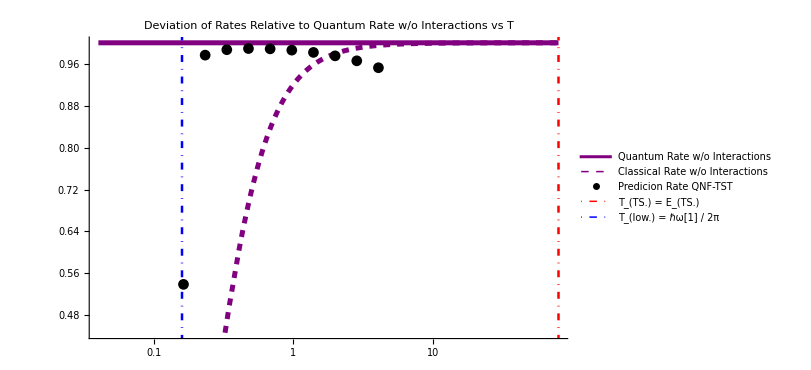

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\plot0.05QNF_4.png

```mathematica
(*Show[
	ListLogPlot[numeratorData, PlotRange -> Full, PlotStyle -> Black],
	LogPlot[numeratorAnalytic[β], {β, βs[[1]], βs[[-1]]}, PlotStyle -> Purple]
]*)

(*ListPlot[integralPartialSumsData, PlotRange -> Full]*)

Show[
	ListLogPlot[rateData, PlotStyle -> Black, PlotLabels->"rateData"],
	LogPlot[rateAnalytic[β], {β, βs[[1]], βs[[-1]]}, PlotStyle -> Purple, PlotLabels->"rateAnalytic"],
	LogPlot[rateAnalyticClassical[β], {β, βs[[1]], βs[[-1]]}, PlotStyle -> {Purple, Dashed}, PlotLabels->"rateAnalyticClassical"]
]

(*plot = Legended[
	Show[
		Plot[
			{1, Evaluate[rateAnalyticClassical[β] / rateAnalytic[β]]},
			{β, 0, 2π},
			PlotStyle -> {Purple, {Purple, Dashed}}
		],
		ListPlot[
			ratioData,
			PlotStyle -> Black
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, Dashed, Line[{{1/barrierEnergy, 0}, {1/barrierEnergy, 2}}]},
					{Blue, Dashed, Line[{{2π, 0}, {2π, 2}}]},
					{Orange, Dashed, Line[{{βs[[1]], 0}, {βs[[1]], 2}}]}
				},
		PlotLabel -> "Deviation of Rates Relative to Quantum Rate w/o Interactions vs β",
		AxesLabel -> {"β"},
		ImageSize -> 500
	],
	{Placed[LineLegend[{Directive[Purple]}, {"     Quantum Rate w/o Interactions"}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed]}, {"Classical Rate w/o Interactions"}], Right],
	PointLegend[{Black}, {"Predicion Rate QNF-TST"}],
	Placed[LineLegend[{Directive[Red, Dashed]}, {"β_(sph.) = 1 / E_(sph.)"}], Right],
	Placed[LineLegend[{Directive[Blue, Dashed]}, {"β_(grd.) = 2π / ℏω[1]"}], Right]}
]

plot2 = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[β] / rateAnalytic[β]]},
			{β, 0, 2π},
			PlotStyle -> {Purple, {Purple, Dashed}}
		],
		ListLogLinearPlot[
			ratioData,
			PlotStyle -> Black
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, Dashed, Line[{{Log[1/barrierEnergy], 0}, {Log[1/barrierEnergy], 2}}]},
					{Blue, Dashed, Line[{{Log[2π], 0}, {Log[2π], 2}}]},
					{Orange, Dashed, Line[{{Log[βs[[1]]], 0}, {Log[βs[[1]]], 2}}]}
				},
		PlotLabel -> "Deviation of Rates Relative to Quantum Rate w/o Interactions vs β",
		AxesLabel -> {"β"},
		ImageSize -> 500
	],
	{Placed[LineLegend[{Directive[Purple]}, {"Quantum Rate w/o Interactions"}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed]}, {"Classical Rate w/o Interactions"}], Right],
	PointLegend[{Black}, {"Predicion Rate QNF-TST"}],
	Placed[LineLegend[{Directive[Red, Dashed]}, {"β_(sph.) = 1 / E_(sph.)"}], Right],
	Placed[LineLegend[{Directive[Blue, Dashed]}, {"β_(grd.) = 2π / ℏω[1]"}], Right]}
]

plot3 = Legended[
	Show[
		Plot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 0, Ts[[-1]]},
			PlotStyle -> {Purple, {Purple, Dashed}}
		],
		ListPlot[
			ratioData2,
			PlotStyle -> Black
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, Dashed, Line[{{barrierEnergy, 0}, {barrierEnergy, 2}}]},
					{Blue, Dashed, Line[{{1/(2π), 0}, {1/(2π), 2}}]},
					{Orange, Dashed, Line[{{Ts[[-1]], 0}, {Ts[[-1]], 2}}]}
				},
		PlotLabel -> "Deviation of Rates Relative to Quantum Rate w/o Interactions vs T",
		AxesLabel -> {"T"},
		ImageSize -> 500
	],
	{Placed[LineLegend[{Directive[Purple]}, {"     Quantum Rate w/o Interactions"}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed]}, {"Classical Rate w/o Interactions"}], Right],
	PointLegend[{Black}, {"Predicion Rate QNF-TST"}],
	Placed[LineLegend[{Directive[Red, Dashed]}, {"T_(sph.) = 1 / E_(sph.)"}], Right],
	Placed[LineLegend[{Directive[Blue, Dashed]}, {"T_(grd.) = 2π / ℏω[1]"}], Right]}
]*)

clippedRatioData = Reverse[{1/#[[1]], #[[2]]} & /@ Select[ratioData, Length[integrals[#[[1]]][[2]]] < numberOfLevels&]]
(*Print[clippedRatioData]*)
txtDir = NotebookDirectory[]~StringJoin~"data"~StringJoin~ToString[ϵ]~StringJoin~"QNF_"~StringJoin~ToString[QNFOrd]~StringJoin~".txt";
Export[txtDir, clippedRatioData]

plot4 = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 1/25, barrierEnergy},
			PlotStyle -> {{Purple, Thickness[0.006]}, {Purple, Dashed, Thickness[0.006]}}
		],
		ListLogLinearPlot[
			clippedRatioData,
			PlotStyle -> Black
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[barrierEnergy], 0}, {Log[barrierEnergy], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}(*,
					{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]},
					{Brown, DotDashed, Thickness[0.003], Line[{{Log[Ts[[-1]]], 0}, {Log[Ts[[-1]]], 2}}]}*)
				},
		PlotLabel -> "Deviation of Rates Relative to Quantum Rate w/o Interactions vs T",
		LabelStyle -> {FontSize -> 16},
		AxesLabel -> {"T"},
		ImageSize -> 600
	],
	{Placed[LineLegend[{Directive[Purple, Thickness[2 0.003]]}, {"Quantum Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[PointLegend[{Black}, {"Predicion Rate QNF-TST"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
	(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω[1]"}, LabelStyle -> {FontSize -> 16}], Right],*)
	Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω[1] / 2π"}, LabelStyle -> {FontSize -> 16}], Right](*,
	Placed[LineLegend[{Directive[Brown, DotDashed, Thickness[2 0.003]]}, {"T_(cut - off) = "~StringJoin~ToString[Ts[[-1]]]}, LabelStyle -> {FontSize -> 16}], Right]*)}
]

imgDir = NotebookDirectory[]~StringJoin~"plot"~StringJoin~ToString[ϵ]~StringJoin~"QNF_"~StringJoin~ToString[QNFOrd]~StringJoin~".png";
Export[imgDir, plot4]
```

```mathematica
(*Data: ϵ = 0.05, Esph = 80.0, cut-off = 50*)
```

```mathematica
(*Data: ϵ = 0.00, Esph = 80.0, cut-off = 50*)
```

```mathematica
(*Data: ϵ = 0.10, Esph = 80.0, cut-off = 50*)
```

## Unclipped Data

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\FULL_DATA_0.05_QNF_4.txt

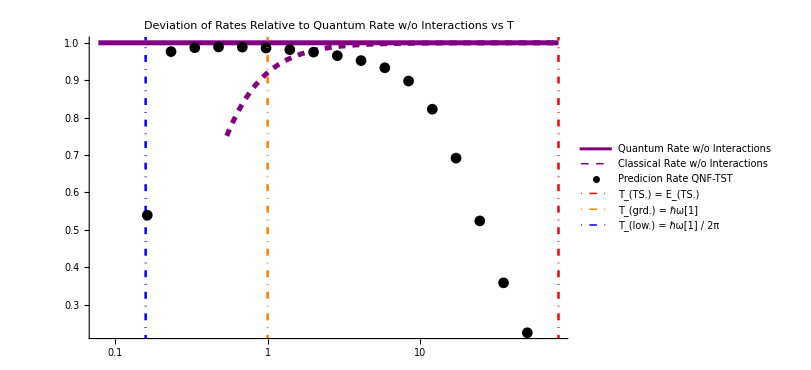

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\FULL_DATA_0.05_QNF_4.png

```mathematica
unclipDir = NotebookDirectory[]~StringJoin~"FULL_DATA_"~StringJoin~ToString[ϵ]~StringJoin~"_QNF_"~StringJoin~ToString[QNFOrd]~StringJoin~".txt";
Export[unclipDir, ratioData2]
unclipped = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 0, barrierEnergy},
			PlotStyle -> {{Purple, Thickness[0.006]}, {Purple, Dashed, Thickness[0.006]}}
		],
		ListLogLinearPlot[
			ratioData2,
			PlotStyle -> Black
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[barrierEnergy], 0}, {Log[barrierEnergy], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}(*,
					{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]},
					{Brown, DotDashed, Thickness[0.003], Line[{{Log[Ts[[-1]]], 0}, {Log[Ts[[-1]]], 2}}]}*)
				},
		PlotLabel -> "Deviation of Rates Relative to Quantum Rate w/o Interactions vs T",
		LabelStyle -> {FontSize -> 16},
		AxesLabel -> {"T"},
		ImageSize -> 600
	],
	{Placed[LineLegend[{Directive[Purple, Thickness[2 0.003]]}, {"Quantum Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[PointLegend[{Black}, {"Predicion Rate QNF-TST"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
	(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω[1]"}, LabelStyle -> {FontSize -> 16}], Right],*)
	Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω[1] / 2π"}, LabelStyle -> {FontSize -> 16}], Right](*,
	Placed[LineLegend[{Directive[Brown, DotDashed, Thickness[2 0.003]]}, {"T_(cut - off) = "~StringJoin~ToString[Ts[[-1]]]}, LabelStyle -> {FontSize -> 16}], Right]*)}
]
imgDir = NotebookDirectory[]~StringJoin~"FULL_DATA_"~StringJoin~ToString[ϵ]~StringJoin~"_QNF_"~StringJoin~ToString[QNFOrd]~StringJoin~".png";
Export[imgDir, unclipped]
```

```mathematica
FullOrd6 = {{0.16313381666919272,0.4104250404821029},
{0.23331659109853312,0.9542590149923228},
{0.3336931164445704,0.974401420280905},
{0.4772532267774492,0.978773744336923},
{0.6825751903315697,0.9778492176372621},
{0.9762299431732065,0.973502630386858},
{1.3962196626059877,0.9660049017433244},
{1.9968956697958025,0.9550937628699523},
{2.855992092681566,0.9403581079888662},
{4.0846855230517445,0.9215072779798006},
{5.841982498825075,0.8976211969364937},
{8.355296711086888,0.8602952617567239},
{11.949878854368283,0.7875433199969547},
{17.090907668735838,0.6630454303514403},
{24.443689220705092,0.5030111131875269},
{34.959754876647146,0.3446275117632134},
{49.99999999999997,0.21651319580786782}};

FullOrd8 = {{0.16313381666919272,0.40952517264850824},
{0.23331659109853312,0.9542356868187717},
{0.3336931164445704,0.9743853946484816},
{0.4772532267774492,0.9787524778863768},
{0.6825751903315697,0.9778110807602629},
{0.9762299431732065,0.9734197952471666},
{1.3962196626059877,0.9658036110183872},
{1.9968956697958025,0.9545880123716323},
{2.855992092681566,0.939064102565292},
{4.0846855230517445,0.9182487330200292},
{5.841982498825075,0.8898430629097478},
{8.355296711086888,0.8445803736370807},
{11.949878854368283,0.7629796566360635},
{17.090907668735838,0.6338077577207974},
{24.443689220705092,0.47543959803587355},
{34.959754876647146,0.3229585930089072},
{49.99999999999997,0.20164764190922313}};

FullError = Abs[FullOrd8- FullOrd6]
Fullpoints = Transpose[{Table[FullOrd6[[k]][[1]], {k, Length[FullOrd6]}],Table[Around[FullOrd6[[k]][[2]],FullError[[k]][[2]]],{k,Length[FullError]}]}]
```

{{0.,0.000899868},{0.,0.0000233282},{0.,0.0000160256},{0.,0.0000212665},{0.,0.0000381369},{0.,0.0000828351},{0.,0.000201291},{0.,0.00050575},{0.,0.00129401},{0.,0.00325854},{0.,0.00777813},{0.,0.0157149},{0.,0.0245637},{0.,0.0292377},{0.,0.0275715},{0.,0.0216689},{0.,0.0148656}}

{{0.163134,0.41040.0009},{0.233317,0.9542590.000023},{0.333693,0.9744010.000016},{0.477253,0.9787740.000021},{0.682575,0.977850.00004},{0.97623,0.973500.00008},{1.39622,0.966000.00020},{1.9969,0.95510.0005},{2.85599,0.94040.0013},{4.08469,0.92150.0033},{5.84198,0.8980.008},{8.3553,0.8600.016},{11.9499,0.7880.025},{17.0909,0.6630.029},{24.4437,0.5030.028},{34.9598,0.3450.022},{50.,0.2170.015}}

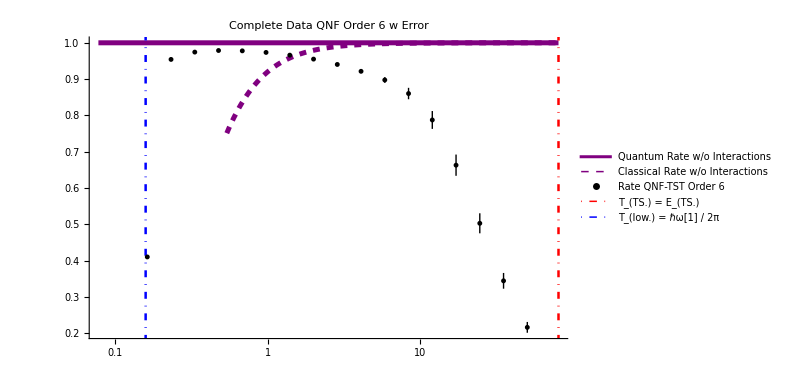

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\QNF 6 Truncation Error_UNCLIPPED.png

```mathematica
PlotTruncUnclipped = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 0, barrierEnergy},
			PlotStyle -> {{Purple, Thickness[0.006]}, {Purple, Dashed, Thickness[0.006]}}
		],
		ListLogLinearPlot[
			Fullpoints,
			PlotStyle -> {Black},
		PlotMarkers-> {Automatic, 5}
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[barrierEnergy], 0}, {Log[barrierEnergy], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}
					(*{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]},
					{Brown, DotDashed, Thickness[0.003], Line[{{Log[Ts[[-1]]], 0}, {Log[Ts[[-1]]], 2}}]}*)
				},
		PlotLabel -> "Complete Data QNF Order 6 w Error",
		LabelStyle -> {FontSize -> 16},
		AxesLabel -> {"T"},
	(*AxesOrigin -> {-2.65926,0.9},*)
		ImageSize -> 600
		(*GridLines -> Automatic*)
	],
	{Placed[LineLegend[{Directive[Purple, Thickness[2 0.003]]}, {"Quantum Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[PointLegend[{Black}, {"Rate QNF-TST Order 6"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
	(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω[1]"}, LabelStyle -> {FontSize -> 16}], Right],*)
	Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω[1] / 2π"}, LabelStyle -> {FontSize -> 16}], Right](*,
	Placed[LineLegend[{Directive[Brown, DotDashed, Thickness[2 0.003]]}, {"T_(cut - off) = "~StringJoin~ToString[Ts[[-1]]]}, LabelStyle -> {FontSize -> 16}], Right]*)}
]

imgDir = NotebookDirectory[]~StringJoin~"QNF 6 Truncation Error_UNCLIPPED"~StringJoin~".png";
Export[imgDir, PlotTruncUnclipped]
```

## Comparing QNF Orders at ϵ = 0.1

{{0.163134,0.417544},{0.233317,0.953895},{0.333693,0.973968},{0.477253,0.978309},{0.682575,0.977237},{0.97623,0.972544},{1.39622,0.964351},{1.9969,0.952112},{2.85599,0.934903},{4.08469,0.911597}}

{{0.163134,0.410425},{0.233317,0.954259},{0.333693,0.974401},{0.477253,0.978774},{0.682575,0.977849},{0.97623,0.973503},{1.39622,0.966005},{1.9969,0.955094},{2.85599,0.940358},{4.08469,0.921507}}

{{0.163134,0.409525},{0.233317,0.954236},{0.333693,0.974385},{0.477253,0.978752},{0.682575,0.977811},{0.97623,0.97342},{1.39622,0.965804},{1.9969,0.954588},{2.85599,0.939064},{4.08469,0.918249}}

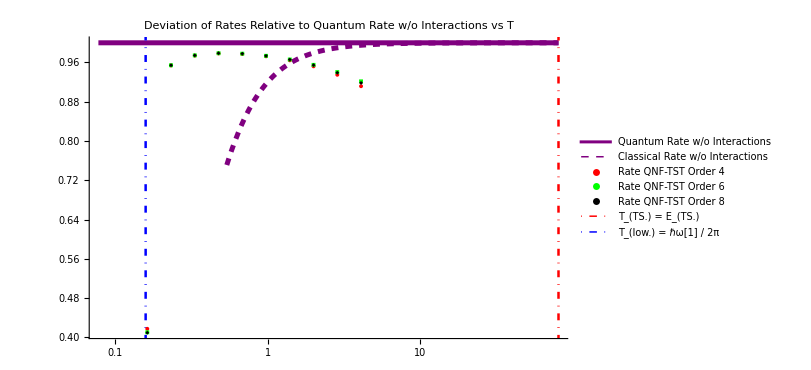

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\QNF Orders.png

```mathematica
Ord4 = {{0.16313381666919272,0.4175444727046693},
{0.23331659109853312,0.9538951994367814},
{0.3336931164445704,0.973967523704727},
{0.4772532267774492,0.9783093704702849},
{0.6825751903315697,0.9772367282520383},
{0.9762299431732065,0.9725435048298537},
{1.3962196626059877,0.9643509425790442},
{1.9968956697958025,0.9521119175543659},
{2.855992092681566,0.9349034494837228},
{4.0846855230517445,0.9115971247466089}}
Ord6 = {{0.16313381666919272,0.4104250404821029},
{0.23331659109853312,0.9542590149923228},
{0.3336931164445704,0.974401420280905},
{0.4772532267774492,0.978773744336923},
{0.6825751903315697,0.9778492176372621},
{0.9762299431732065,0.973502630386858},
{1.3962196626059877,0.9660049017433244},
{1.9968956697958025,0.9550937628699523},
{2.855992092681566,0.9403581079888662},
{4.0846855230517445,0.9215072779798006}}
Ord8 = {{0.16313381666919272,0.40952517264850824},
{0.23331659109853312,0.9542356868187717},
{0.3336931164445704,0.9743853946484816},
{0.4772532267774492,0.9787524778863768},
{0.6825751903315697,0.9778110807602629},
{0.9762299431732065,0.9734197952471666},
{1.3962196626059877,0.9658036110183872},
{1.9968956697958025,0.9545880123716323},
{2.855992092681566,0.939064102565292},
{4.0846855230517445,0.9182487330200292}}

orders = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 0, barrierEnergy},
			PlotStyle -> {{Purple, Thickness[0.006]}, {Purple, Dashed, Thickness[0.006]}}
		],
		ListLogLinearPlot[
			{Ord4,Ord6,Ord8},
		PlotMarkers->{Automatic, Tiny},
			PlotStyle -> {Red, Green, Black}
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[barrierEnergy], 0}, {Log[barrierEnergy], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}(*,
					{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]},
					{Brown, DotDashed, Thickness[0.003], Line[{{Log[Ts[[-1]]], 0}, {Log[Ts[[-1]]], 2}}]}*)
				},
		PlotLabel -> "Deviation of Rates Relative to Quantum Rate w/o Interactions vs T",
		LabelStyle -> {FontSize -> 16},
		AxesLabel -> {"T"},
		ImageSize -> 600
		(*GridLines -> Automatic*)
	],
	{Placed[LineLegend[{Directive[Purple, Thickness[2 0.003]]}, {"Quantum Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[PointLegend[{Red, Green, Black}, {"Rate QNF-TST Order 4","Rate QNF-TST Order 6","Rate QNF-TST Order 8"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
	(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω[1]"}, LabelStyle -> {FontSize -> 16}], Right],*)
	Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω[1] / 2π"}, LabelStyle -> {FontSize -> 16}], Right](*,
	Placed[LineLegend[{Directive[Brown, DotDashed, Thickness[2 0.003]]}, {"T_(cut - off) = "~StringJoin~ToString[Ts[[-1]]]}, LabelStyle -> {FontSize -> 16}], Right]*)}
]
imgDir = NotebookDirectory[]~StringJoin~"QNF Orders"~StringJoin~".png";
Export[imgDir, orders]
```

## Comparing Coupling Strengths at QNF Order 4

{{0.163134,0.538963},{0.233317,0.976467},{0.333693,0.986849},{0.477253,0.989037},{0.682575,0.98845},{0.97623,0.985993},{1.39622,0.981653},{1.9969,0.975082},{2.85599,0.965621},{4.08469,0.95241}}

{{0.163134,0.417544},{0.233317,0.953895},{0.333693,0.973968},{0.477253,0.978309},{0.682575,0.977237},{0.97623,0.972544},{1.39622,0.964351},{1.9969,0.952112},{2.85599,0.934903},{4.08469,0.911597}}

{{0.163134,0.304559},{0.233317,0.911345},{0.333693,0.948976},{0.477253,0.957512},{0.682575,0.955709},{0.97623,0.947133},{1.39622,0.93233},{1.9969,0.910784},{2.85599,0.881578},{4.08469,0.843794}}

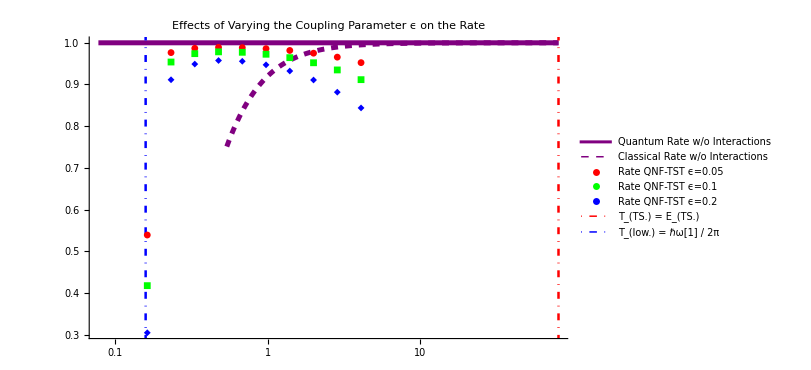

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\Coupling Strengths Rate Effects.png

```mathematica
eps05 = {{0.16313381666919272,0.538962766874178},
{0.23331659109853312,0.9764674477416192},
{0.3336931164445704,0.9868485605118765},
{0.4772532267774492,0.9890371985405616},
{0.6825751903315697,0.9884498076094246},
{0.9762299431732065,0.9859933189443175},
{1.3962196626059877,0.981653456789368},
{1.9968956697958025,0.9750817933148295},
{2.855992092681566,0.9656209470201903},
{4.0846855230517445,0.9524103366056087}}
eps1 = {{0.16313381666919272,0.4175444727046693},
{0.23331659109853312,0.9538951994367814},
{0.3336931164445704,0.973967523704727},
{0.4772532267774492,0.9783093704702849},
{0.6825751903315697,0.9772367282520383},
{0.9762299431732065,0.9725435048298537},
{1.3962196626059877,0.9643509425790442},
{1.9968956697958025,0.9521119175543659},
{2.855992092681566,0.9349034494837228},
{4.0846855230517445,0.9115971247466089}}
eps2 = {{0.16313381666919272,0.30455900647156836},
{0.23331659109853312,0.9113448569360337},
{0.3336931164445704,0.9489761089952287},
{0.4772532267774492,0.9575123057027932},
{0.6825751903315697,0.9557087737207001},
{0.9762299431732065,0.947132662762971},
{1.3962196626059877,0.9323300141612089},
{1.9968956697958025,0.9107844786734044},
{2.855992092681566,0.8815775149863553},
{4.0846855230517445,0.8437937812016528}}
couplings = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 0, barrierEnergy},
			PlotStyle -> {{Purple, Thickness[0.006]}, {Purple, Dashed, Thickness[0.006]}}
		],
		ListLogLinearPlot[
			{eps05,eps1,eps2},
			PlotStyle -> {Red, Green, Blue},
		PlotMarkers->{Automatic,Small}
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[barrierEnergy], 0}, {Log[barrierEnergy], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}(*,
					{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]},
					{Brown, DotDashed, Thickness[0.003], Line[{{Log[Ts[[-1]]], 0}, {Log[Ts[[-1]]], 2}}]}*)
				},
		PlotLabel -> "Effects of Varying the Coupling Parameter ϵ on the Rate",
		LabelStyle -> {FontSize -> 16},
		AxesLabel -> {"T"},
		ImageSize -> 600
		(*GridLines -> Automatic*)
	],
	{Placed[LineLegend[{Directive[Purple, Thickness[2 0.003]]}, {"Quantum Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[PointLegend[{Red, Green, Blue}, {"Rate QNF-TST ϵ=0.05","Rate QNF-TST ϵ=0.1","Rate QNF-TST ϵ=0.2"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
	(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω[1]"}, LabelStyle -> {FontSize -> 16}], Right],*)
	Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω[1] / 2π"}, LabelStyle -> {FontSize -> 16}], Right](*,
	Placed[LineLegend[{Directive[Brown, DotDashed, Thickness[2 0.003]]}, {"T_(cut - off) = "~StringJoin~ToString[Ts[[-1]]]}, LabelStyle -> {FontSize -> 16}], Right]*)}
]
imgDir = NotebookDirectory[]~StringJoin~"Coupling Strengths Rate Effects"~StringJoin~".png";
Export[imgDir, couplings]
```

## Truncation Error for QNF Order 6

```mathematica
Error = Abs[Ord8- Ord6]
allpoints = Transpose[{Table[Ord6[[i]][[1]], {i, Length[Ord6]}],Table[Around[Ord6[[i]][[2]],Error[[i]][[2]]],{i,Length[Ord6]}]}];
data1 = allpoints[[1]]
datarest = allpoints[[2;;]]
```

{{0.,0.000899868},{0.,0.0000233282},{0.,0.0000160256},{0.,0.0000212665},{0.,0.0000381369},{0.,0.0000828351},{0.,0.000201291},{0.,0.00050575},{0.,0.00129401},{0.,0.00325854}}

{0.163134,0.41040.0009}

{{0.233317,0.9542590.000023},{0.333693,0.9744010.000016},{0.477253,0.9787740.000021},{0.682575,0.977850.00004},{0.97623,0.973500.00008},{1.39622,0.966000.00020},{1.9969,0.95510.0005},{2.85599,0.94040.0013},{4.08469,0.92150.0033}}

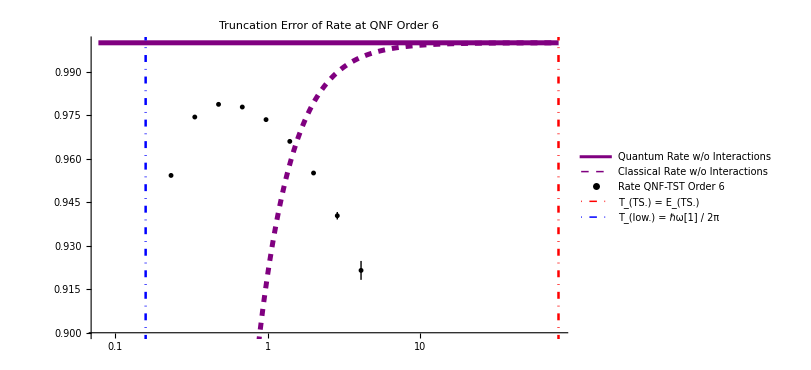

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\plot_QNF 6 Truncation Error_Zoomed.png

```mathematica
PlotTrunc = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 0, barrierEnergy},
			PlotStyle -> {{Purple, Thickness[0.006]}, {Purple, Dashed, Thickness[0.006]}}
		],
		ListLogLinearPlot[
			allpoints,
			PlotStyle -> {Black},
		PlotMarkers-> {Automatic, 5}
	],
		PlotRange -> {0.9,1},
		Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[barrierEnergy], 0}, {Log[barrierEnergy], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}(*,
					{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]},
					{Brown, DotDashed, Thickness[0.003], Line[{{Log[Ts[[-1]]], 0}, {Log[Ts[[-1]]], 2}}]}*)
				},
		PlotLabel -> "Truncation Error of Rate at QNF Order 6",
		LabelStyle -> {FontSize -> 16},
		AxesLabel -> {"T"},
	AxesOrigin -> {-2.65926,0.9},
		ImageSize -> 600
		(*GridLines -> Automatic*)
	],
	{Placed[LineLegend[{Directive[Purple, Thickness[2 0.003]]}, {"Quantum Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[PointLegend[{Black}, {"Rate QNF-TST Order 6"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
	(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω[1]"}, LabelStyle -> {FontSize -> 16}], Right],*)
	Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω[1] / 2π"}, LabelStyle -> {FontSize -> 16}], Right](*,
	Placed[LineLegend[{Directive[Brown, DotDashed, Thickness[2 0.003]]}, {"T_(cut - off) = "~StringJoin~ToString[Ts[[-1]]]}, LabelStyle -> {FontSize -> 16}], Right]*)}
]

imgDir = NotebookDirectory[]~StringJoin~"plot_"~StringJoin~"QNF 6 Truncation Error_Zoomed"~StringJoin~".png";
Export[imgDir, PlotTrunc]
```

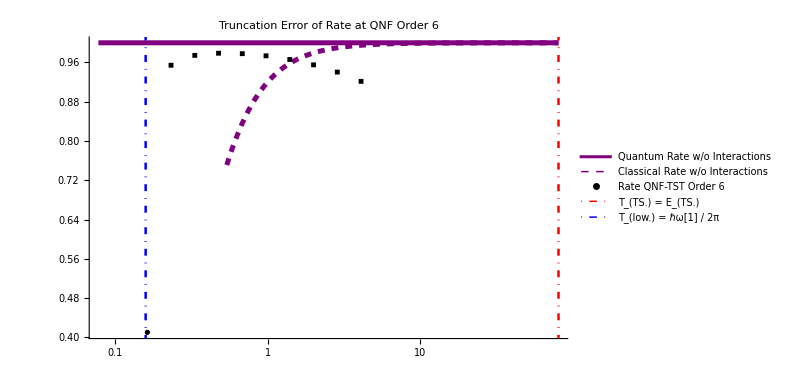

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (OLD)\plot_QNF 6 Truncation Error_Full Range.png

```mathematica
PlotTruncFull = Legended[
	Show[
		LogLinearPlot[
			{1, Evaluate[rateAnalyticClassical[1/T] / rateAnalytic[1/T]]},
			{T, 0, barrierEnergy},
			PlotStyle -> {{Purple, Thickness[0.006]}, {Purple, Dashed, Thickness[0.006]}}
		],
		ListLogLinearPlot[
			{{data1},datarest},
			PlotStyle -> {Black,Black},
		PlotMarkers-> {Automatic, 5}
	],
		PlotRange -> Full,
		Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[barrierEnergy], 0}, {Log[barrierEnergy], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}(*,
					{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]},
					{Brown, DotDashed, Thickness[0.003], Line[{{Log[Ts[[-1]]], 0}, {Log[Ts[[-1]]], 2}}]}*)
				},
		PlotLabel -> "Truncation Error of Rate at QNF Order 6",
		LabelStyle -> {FontSize -> 16},
		AxesLabel -> {"T"},
	(*AxesOrigin -> {-2.65926,0.9},*)
		ImageSize -> 600
		(*GridLines -> Automatic*)
	],
	{Placed[LineLegend[{Directive[Purple, Thickness[2 0.003]]}, {"Quantum Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[PointLegend[{Black}, {"Rate QNF-TST Order 6"}, LabelStyle -> {FontSize -> 16}], Right],
	Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
	(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω[1]"}, LabelStyle -> {FontSize -> 16}], Right],*)
	Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω[1] / 2π"}, LabelStyle -> {FontSize -> 16}], Right](*,
	Placed[LineLegend[{Directive[Brown, DotDashed, Thickness[2 0.003]]}, {"T_(cut - off) = "~StringJoin~ToString[Ts[[-1]]]}, LabelStyle -> {FontSize -> 16}], Right]*)}
]

imgDir = NotebookDirectory[]~StringJoin~"plot_"~StringJoin~"QNF 6 Truncation Error_Full Range"~StringJoin~".png";
Export[imgDir, PlotTruncFull]
```